## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2024\PAPER II\alpha 0.84\parity integer half integer

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,F];

Sz[J_]:=Sz[J]=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=SM[J]=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=Sm[J]=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=Sx[J]=(1/2)(SM[J]+Sm[J]);

(*F[J_,α_,k_]:=MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α)(Sz[J])];*)
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];

Clear[Tq];
Tq[q_]:=Module[{a,b,points=allpointsx[[q]]},
{a,b}=CoefficientList[Fit[points,{1,x},x],x];
{qlist[[q]],-b}
];

Clear[IPR];
IPR[J_,q_,ini_]:=Module[{a},
Log[Sum[Chop[Abs[Chop[Conjugate[eigen[[j]]],10^(-MachinePrecision)].Chop[ini,10^(-MachinePrecision)]]^(2q),10^(-MachinePrecision)],{j,1,2J+1}]]
];

Clear[a2];
a2[J_,Q_,P_]:=a2[J,Q,P]=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

# Integer J phase space parities

```mathematica
radius=1.99999;
delta=0.03;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=Select[gridPoints,Abs[Norm[#]^2-radius^2]<=2-1.99999&];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

13952

```mathematica
ListPlot[region,AspectRatio->1];
```

```mathematica
Clear[J];
J=100;
α=0.84;
τ=1;
k=1.3;
```

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],20]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],20]]
];
```

```mathematica
cohesM=ParallelTable[Quiet[a2iM[J,i[[1]],i[[2]]]],{i,region}];
cohesm=ParallelTable[Quiet[a2im[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];
```

```mathematica
cohesfloqiM=ParallelTable[Conjugate[eigenvecM].i,{i,cohesM}];
ipriM=ParallelTable[Total[Abs[i]^4],{i,cohesfloqiM}];
cohesfloqim=ParallelTable[Conjugate[eigenvecm].i,{i,cohesm}];
iprim=ParallelTable[Total[Abs[i]^4],{i,cohesfloqim}];
```

```mathematica
newdataM=Table[{region[[i,1]],region[[i,2]],-Log[ipriM[[i]]]/Log[2J+1]},{i,Length[region]}];
newdatam=Table[{region[[i,1]],region[[i,2]],-Log[iprim[[i]]]/Log[2J+1]},{i,Length[region]}];
```

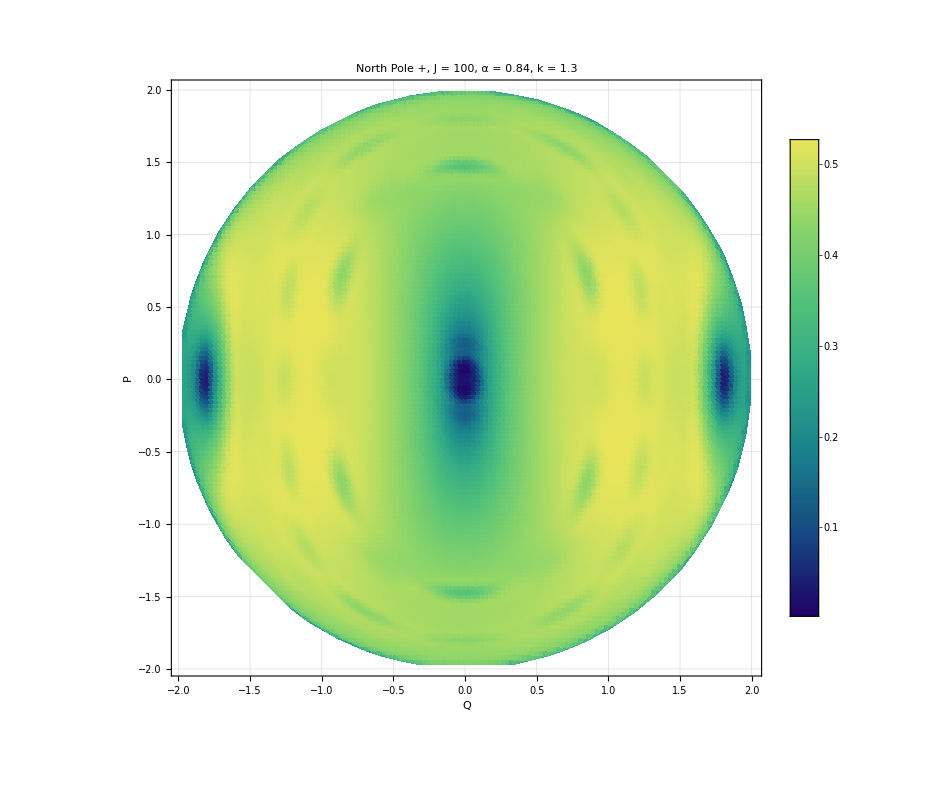

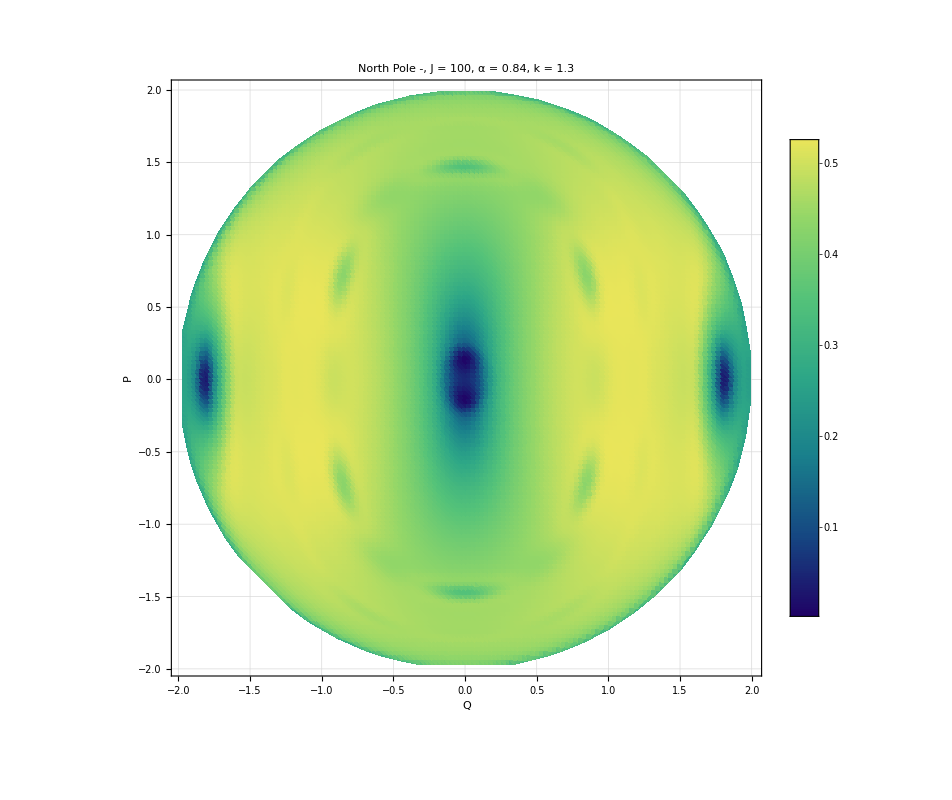

```mathematica
a=ListDensityPlot[newdataM,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Pole +, J = 100, α = 0.84, k = "<>ToString[k],40,Black],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800,ColorFunction->"BlueGreenYellow"]
Export["plot11.jpg",a,ImageResolution->300];
a=ListDensityPlot[newdatam,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Pole -, J = 100, α = 0.84, k = "<>ToString[k],40,Black],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800,ColorFunction->"BlueGreenYellow"]
Export["plot12.jpg",a,ImageResolution->300];
```

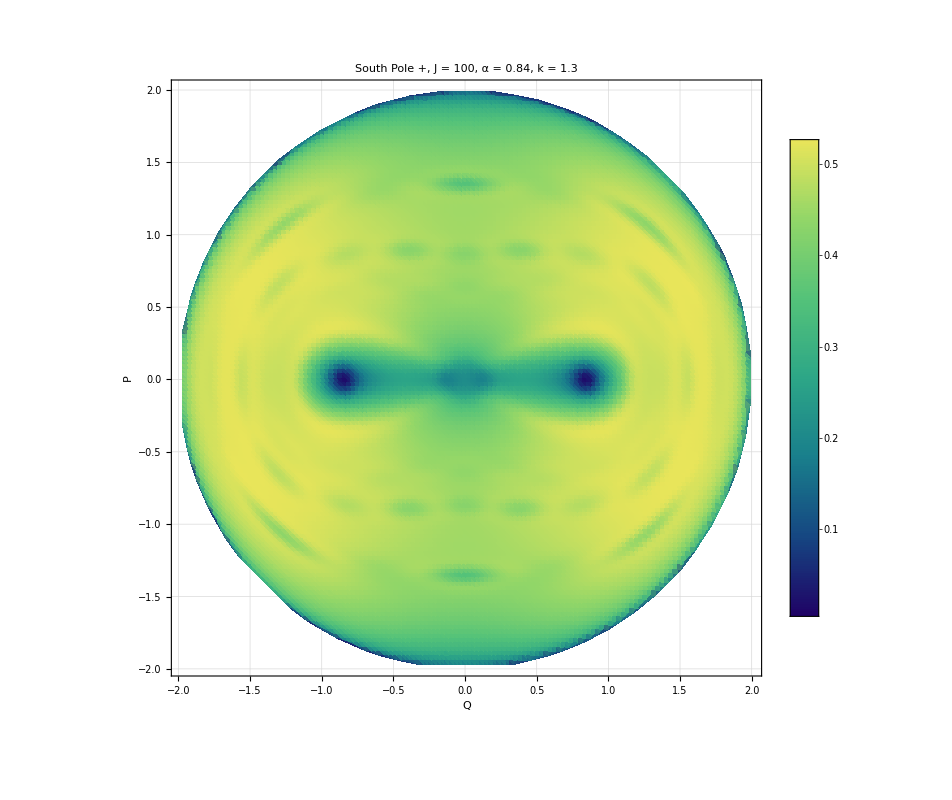

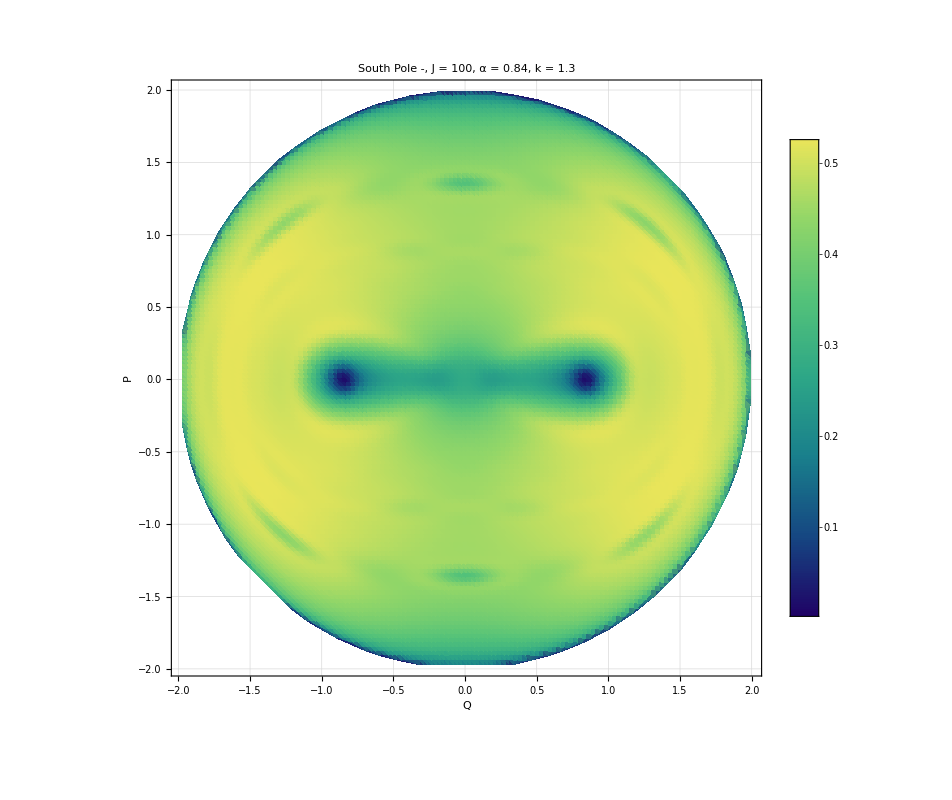

```mathematica
a=ListDensityPlot[newdataM,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["South Pole +, J = 100, α = 0.84, k = "<>ToString[k],40,Black],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800,ColorFunction->"BlueGreenYellow"]
Export["plot13.jpg",a,ImageResolution->300];
a=ListDensityPlot[newdatam,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["South Pole -, J = 100, α = 0.84, k = "<>ToString[k],40,Black],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800,ColorFunction->"BlueGreenYellow"]
Export["plot14.jpg",a,ImageResolution->300];
```